```mathematica
(*Limpiamos memoria*)
Clear["Global`*"]
```

## Práctica 1

## EJERCICIO 1

### Calcula la aproximación decimal de la siguiente expresión (log_3 2)−(e^2 sin(35.ba))/(√3−1) con 9 dígitos decimales

```mathematica
N[(Log[3,2]-(E^2Sin[35Degree])/(Sqrt[3]-1)),10]
```

-5.158543356

## EJERCICIO 2

### a) Genera una lista con los cuadrados de los 100 primeros números pares. b) Calcula el elemento 89 de la lista

```mathematica
l2=Range[2,200,2]^2
```

{4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000,10404,10816,11236,11664,12100,12544,12996,13456,13924,14400,14884,15376,15876,16384,16900,17424,17956,18496,19044,19600,20164,20736,21316,21904,22500,23104,23716,24336,24964,25600,26244,26896,27556,28224,28900,29584,30276,30976,31684,32400,33124,33856,34596,35344,36100,36864,37636,38416,39204,40000}

```mathematica
l2[[89]]
```

31684

## EJERCICIO 3

### 3) Sean las funciones f(x)=xsin(3x)+2^(1/5)/(x−4) y g(x,y)=xsin(2xy)+x/(x+y) a) Define f(x) b)Define g(x) c) Calcula el valor exacto y aproximado de f(6) d) Calcula el valor exacto y aproximado de g(π,2π)

```mathematica
f[x_]:=x*Sin[3x]+(Surd[2,5])/(x-4)
g[x_,y_]:=x*Sin[2x y ]+(x)/(x+y)
```

```mathematica
f[6.]
```

-3.93157

```mathematica
f[6]
```

1/2^(4/5)+6 Sin[18]

```mathematica
g[Pi,2Pi]//N
```

3.40688

```mathematica
g[Pi,2Pi]
```

1/3+π Sin[4 π^2]

## EJERCICIO 4

### 4) Dibuja en el mismo gráfico las funciones f(x)=x/2^x y g(x)=√(x^2+1) en el intervalo (0, 3π) utilizando los colores marrón y naranja.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=x/(2^x)
g[x_]:=Sqrt[(x^2+1)]
```

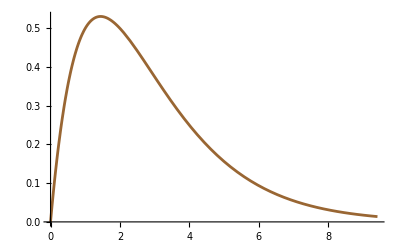

```mathematica
Plot[{f[x]},{x,0,3*Pi},PlotStyle->{Brown}]
```

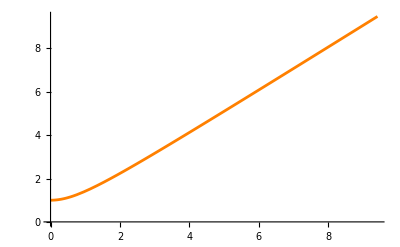

```mathematica
Plot[g[x],{x,0,3*Pi},PlotStyle->{Orange}]
```